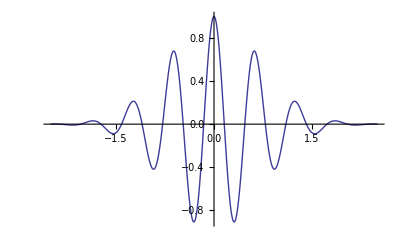

Block::lvset: Local variable specification {t = 1, ω_0 = 7} contains ω_0 = 7, which is an assignment to ω_0; only assignments to symbols are allowed.

```mathematica
Clear[e, tT, t, omega]

e[t_] := E^(-t^2/tT^2) Cos[ omega t ]

Plot[ Block[{tT=1,omega=10},e[t]],{t,-2.5,2.5}]
```

```mathematica
ft[ω_] = Distribute[FullSimplify[FourierTransform[ e[t], t, ω]]]
```

(ⅇ^(-1/4 tT^2 (omega+ω)^2))/(2 √2 √(1/tT^2))+(ⅇ^(omega tT^2 ω-1/4 tT^2 (omega+ω)^2))/(2 √2 √(1/tT^2))

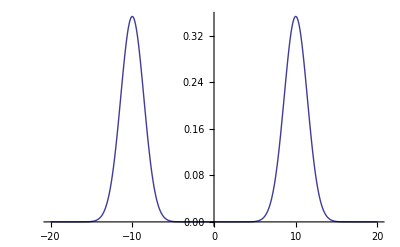

```mathematica
Plot[ Block[{tT=1,omega=10},ft[ω]],{ω,-20,20}]
```

```mathematica
Plot[1.1Tanh[x] + 1.3, {x, -10, 10}]
```

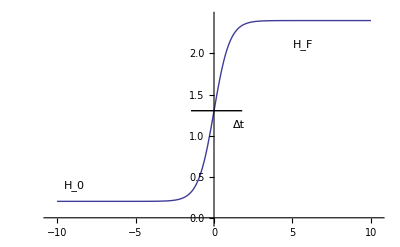

```mathematica
Plot[{ x^2, 2 x^2, 30 E^{-x^2/2}}, {x, -5, 5}]
```